```mathematica
(* KM07 equation 17 and 18 *)
coefu=kb^4*T^4/(2*Pi^2*hbar^3*c^3)
coefu//.{T->T11*10^(11)}
```

5.82536×10^-16 T^4

5.82536×10^28 T11^4

```mathematica
coefn=kb^3*T^3/(2*Pi^2*hbar^3*c^3)
coefn//.{T->T11*10^(11)}
```

4.21927 T^3

4.21927×10^33 T11^3

```mathematica
F[m_,eta_]:=NIntegrate[x^m/(Exp[x-eta]+1),{x,0,Infinity}]
```

```mathematica
one=coefu*F[3,0]
two=coefn*F[2,0]
rat=one/two
rattest=kb*T
rat/rattest
```

3.31009×10^-15 T^4

7.6077 T^3

4.35097×10^-16 T

1.38066×10^-16 T

3.15137

```mathematica
coefu/coefn/(kb*T)
```

1.

```mathematica
F[3,0]/F[2,0]
```

3.15137

```mathematica
one=coefu*F[3,0]//.{T->10^(10)}
two=coefn*F[2,0]//.{T->10^(10)}
rat=one/two/ergPmev
```

3.31049×10^25

7.60839×10^30

2.71574

```mathematica
(* tauabs *)
```

```mathematica
1/(c*coefu*F[3,0])//.{T->T11*10^(11)}
```

(1.0076×10^-40)/T11^4

```mathematica
1/(2*1.0075975386739164*^-40)
```

4.9623×10^39

```mathematica
1*1/(1.98*10^(40))
```

5.05051×10^-41

```mathematica
2/(7/2*sigmasb*T^4//.{T->T11*10^(11)})
```

(1.0076×10^-40)/T11^4

```mathematica
F[5,0.0]
```

118.266

```mathematica
(* Plasmon process *)
```

```mathematica
sigma0=1.76*10^(-44)
alphastar=1/137
gamma0=5.565*10^(-2)
gamma=gamma0*((Pi^2+3*etae^2)/3)^(1/2)
sinTw=0.23

cv=1/2+2*sinTw (* for electron type *)
pre=1.0

(*
cv =-1/2+2*sinTw (* for mu and tau types each *)
pre=4.0
*)
Rnue=pre*Pi^3/(6*alphastar)*cv^2*sigma0*c/(me*c^2)^2*(kb*T)^8/(2*Pi*hbar*c)^6
Rnue//.{T->T11*10^(11)}
Qnue=pre*Pi^3/(6*alphastar)*cv^2*sigma0*c/(me*c^2)^2*(kb*T)^9/(2*Pi*hbar*c)^6
Qnue//.{T->T11*10^(11)}
```

1.76×10^-44

1/137

0.05565

0.0321295 √(3 etae^2+π^2)

0.23

0.96

1.

1.10399×10^-51 T^8

1.10399×10^37 T11^8

1.52428×10^-67 T^9

1.52428×10^32 T11^9

```mathematica
p=4
term0=Normal[Series[Integrate[x^p/(Exp[x-eta]+1),{x,0,Infinity}],{eta,0,5}]]
terminf=Normal[Series[Integrate[x^p/(Exp[x-eta]+1),{x,0,Infinity}],{eta,Infinity,5}]]
termneginf=Normal[Series[Integrate[x^p/(Exp[x-eta]+1),{x,0,Infinity}],{eta,-Infinity,5}]]
termrest=Normal[Series[Integrate[x^p/(Exp[x-eta]+1),{x,0,Infinity}]-term0*Exp[-eta],{eta,0,1}]]
```

4

eta^5/10+(eta^3 π^2)/3+(7 eta π^4)/30+eta^4 Log[2]+9 eta^2 Zeta[3]+(45 Zeta[5])/2

1/32400000 ⅇ^(-5 eta) (248832-759375 ⅇ^eta+3200000 ⅇ^(2 eta)-24300000 ⅇ^(3 eta)+777600000 ⅇ^(4 eta)+ⅇ^(5 eta) (6480000 eta^5+21600000 eta^3 π^2+15120000 eta π^4))

-24 (-ⅇ^eta+ⅇ^(2 eta)/32-ⅇ^(3 eta)/243+ⅇ^(4 eta)/1024-ⅇ^(5 eta)/3125+ⅇ^(6 eta)/7776)

45/2 eta Zeta[5]

```mathematica
terminfpart=terminf
term0part=term0
termfinal=FullSimplify[term0*Exp[-eta]+terminf*(1-Exp[-eta])]
(*termfinal=FullSimplify[term0*Exp[-eta]+terminf*)
```

1/32400000 ⅇ^(-5 eta) (248832-759375 ⅇ^eta+3200000 ⅇ^(2 eta)-24300000 ⅇ^(3 eta)+777600000 ⅇ^(4 eta)+ⅇ^(5 eta) (6480000 eta^5+21600000 eta^3 π^2+15120000 eta π^4))

eta^5/10+(eta^3 π^2)/3+(7 eta π^4)/30+eta^4 Log[2]+9 eta^2 Zeta[3]+(45 Zeta[5])/2

1/32400000 ⅇ^(-6 eta) (-248832+ⅇ^eta (1008207+625 ⅇ^eta (-6335+32 ⅇ^eta (1375+27 ⅇ^eta (-1485+2 ⅇ^eta (720+(-3+6 ⅇ^eta) eta^5+10 (-1+2 ⅇ^eta) eta^3 π^2+7 (-1+2 ⅇ^eta) eta π^4+30 eta^4 Log[2]+270 eta^2 Zeta[3]+675 Zeta[5]))))))

```mathematica
termfinalneg=FullSimplify[term0*Exp[eta]+termneginf*(1-Exp[eta])]
```

-24 (1-ⅇ^eta) (-ⅇ^eta+ⅇ^(2 eta)/32-ⅇ^(3 eta)/243+ⅇ^(4 eta)/1024-ⅇ^(5 eta)/3125+ⅇ^(6 eta)/7776)+1/30 ⅇ^eta (7 eta π^4+675 Zeta[5])

```mathematica
termneginf//.{eta->0.0}
term0//.{eta->0.0}
```

23.3299

23.3309

```mathematica
x0=-4.0
termfinal//.{eta->x0}
termneginf//.{eta->x0}
termfinalneg//.{eta->x0}
F[p,x0]
```

-4.

-1.8932×10^8

0.439324

-0.806571

0.439324

```mathematica
termfinal
```

1/32400000 ⅇ^(-6 eta) (-248832+ⅇ^eta (1008207+625 ⅇ^eta (-6335+32 ⅇ^eta (1375+27 ⅇ^eta (-1485+2 ⅇ^eta (720+(-3+6 ⅇ^eta) eta^5+10 (-1+2 ⅇ^eta) eta^3 π^2+7 (-1+2 ⅇ^eta) eta π^4+30 eta^4 Log[2]+270 eta^2 Zeta[3]+675 Zeta[5]))))))

```mathematica
FullSimplify[termfinal]
```

1/32400000 ⅇ^(-6 eta) (-248832+ⅇ^eta (1008207+625 ⅇ^eta (-6335+32 ⅇ^eta (1375+27 ⅇ^eta (-1485+2 ⅇ^eta (720+(-3+6 ⅇ^eta) eta^5+10 (-1+2 ⅇ^eta) eta^3 π^2+7 (-1+2 ⅇ^eta) eta π^4+30 eta^4 Log[2]+270 eta^2 Zeta[3]+675 Zeta[5]))))))

```mathematica
FortranForm[termfinal]
```

(-248832 + E**eta*(1008207 + 
     -       625*E**eta*(-6335 + 32*E**eta*
     -           (1375 + 27*E**eta*(-1485 + 
     -                2*E**eta*(720 + (-3 + 6*E**eta)*eta**5 + 
     -                   10*(-1 + 2*E**eta)*eta**3*Pi**2 + 7*(-1 + 2*E**eta)*eta*Pi**4 + 
     -                   30*eta**4*Log(2) + 270*eta**2*Zeta(3) + 675*Zeta(5)))))))/
     -  (3.24e7*E**(6*eta))

```mathematica
FortranForm[termneginf]
```

-24*(-E**eta + E**(2*eta)/32. - E**(3*eta)/243. + E**(4*eta)/1024. - 
     -    E**(5*eta)/3125. + E**(6*eta)/7776.)

```mathematica
F[3,0.0]
F[4,0.0]
F[5,0.0]
```

5.6822

23.3309

118.266

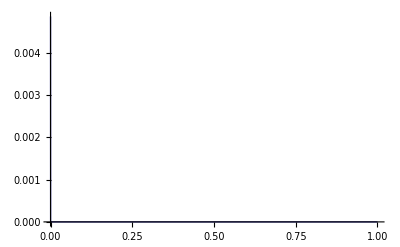

```mathematica
Plot[x^5/(Exp[x]+1),{x,0,10^9}]
```

```mathematica
x^5/(Exp[x]+1)//.{x->10^9}
```

1000000000000000000000000000000000000000000000/(1+ⅇ^1000000000)

```mathematica
Exp[1000.0]
```

1.97007111402×10^434

```mathematica
FortranForm[termfinal//.{ⅇ->myEXP}]
```

(-248832 + myEXP**eta*(1008207 + 
     -       625*myEXP**eta*(-6335 + 32*myEXP**eta*
     -           (1375 + 27*myEXP**eta*(-1485 + 
     -                2*myEXP**eta*(720 + 6*eta**5*(-1 + myEXP**eta) + 
     -                   20*eta**3*(-1 + myEXP**eta)*Pi**2 + 7*eta*(-1 + 2*myEXP**eta)*Pi**4 + 
     -                   675*Zeta(5)))))))/(3.24e7*myEXP**(6*eta))

```mathematica
N[Log[2],15]
N[Zeta[5],15]
```

0.693147180559945

1.03692775514337

```mathematica
FortranForm[N[termneginf]]
```

-24.*(-1.*2.718281828459045**eta + 0.03125*2.718281828459045**(2.*eta) - 
     -    0.00411522633744856*2.718281828459045**(3.*eta) + 
     -    0.0009765625*2.718281828459045**(4.*eta) - 0.00032*2.718281828459045**(5.*eta) + 
     -    0.0001286008230452675*2.718281828459045**(6.*eta))

```mathematica
FortranForm[N[termfinal]]
```

(3.08641975308642e-8*(-248832. + 
     -      2.718281828459045**eta*(1.008207e6 + 
     -         625.*2.718281828459045**eta*
     -          (-6335. + 32.*2.718281828459045**eta*
     -             (1375. + 27.*2.718281828459045**eta*
     -                (-1485. + 2.*2.718281828459045**eta*
     -                   (1419.9262347217746 + 
     -                     681.863637238017*(-1. + 2.*2.718281828459045**eta)*eta + 
     -                     197.39208802178717*(-1. + 2.718281828459045**eta)*eta**3 + 
     -                     6.*(-1. + 2.718281828459045**eta)*eta**5)))))))/
     -  2.718281828459045**(6.*eta)

```mathematica
terminf//.{eta->0}
```

-6+(7 π^4)/60

```mathematica
F3fit[0]
```

(7 π^4)/120

```mathematica
4*15
```

60

```mathematica
(* Liebendorfer 2005 *)
```

```mathematica
N[Zeta[3],15]
alpha=N[2*Pi^2/(9*Zeta[3])-1,15]
F2fit[eta_]:=1/3*(eta^3+Pi^2*eta)+3/2*Zeta[3]*Exp[-alpha*eta]
F3fit[eta_]:=1/4*(eta^4+2*Pi^2*eta^2+7*Pi^4/15)-7*Pi^4/120*Exp[-eta]
F4fit[eta_]:=1/5*(eta^5+3*Pi^2*eta^3+7*Pi^4*eta/15+45*Zeta[5]*5)-45*Zeta[5]/2*Exp[-eta]
F5fit[eta_]:=1/6*(eta^6+5*Pi^2*eta^4+7*Pi^4*eta^2+31*Pi^6/21)-31*Pi^6/252*Exp[-eta]
```

1.20205690315959

0.824577036826941

```mathematica
F3fit[0]
```

(7 π^4)/120

0

0.1

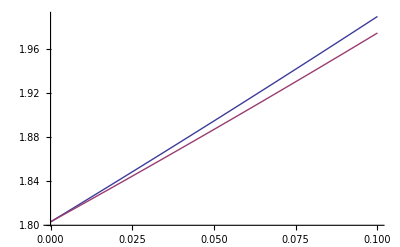

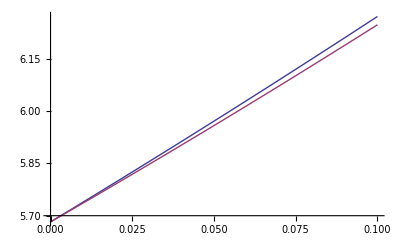

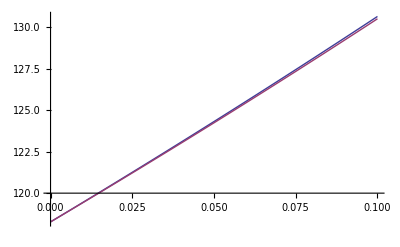

```mathematica
xinner=0
xouter=.1
Plot[{F2fit[x],F[2,x]},{x,xinner,xouter}]
Plot[{F3fit[x],F[3,x]},{x,xinner,xouter}]
Plot[{F5fit[x],F[5,x]},{x,xinner,xouter}]
```

```mathematica
etanu=0
etaantinu=0
unu0=(7 (arad/F[3,0]) T^4)/16*F[3,etanu]
uantinu0=(7 (arad/F[3,0]) T^4)/16*F[3,etaantinu]
utotnu0=unu0+uantinu0
Qnu0=(2*c/4)*unu0
Qantinu0=(2*c/4)*uantinu0
Qtotnu0=(2*c/4)*utotnu0
```

0

0

3.31049×10^-15 T^4

3.31049×10^-15 T^4

6.62098×10^-15 T^4

0.000049623 T^4

0.000049623 T^4

0.000099246 T^4

```mathematica
(* Kaz *)
```

```mathematica
Qkaz=(7/8)*sigmasb*T^4
uradkaz=Qkaz/c*4
```

0.000049623 T^4

6.62098×10^-15 T^4

```mathematica
nnu0=(7 (arad/F[3,0]) T^4)/(16*(kb*T))*F[2,etanu]
Fnu0=(1*c/4)*nnu0
```

7.60839 T^3

5.70235×10^10 T^3

```mathematica
tauabs=qminus/(2*c*unu0)//.{T->T11*10^(11)}
```

(5.03799×10^-41 qminus)/T11^4

```mathematica
tauabskaz=qminus*H/((7/2)*sigmasb*T^4)//.{T->T11*10^(11)}
```

(5.03799×10^-41 H qminus)/T11^4